## Initializing Truncated Theta Functions (Run First)

```mathematica
thetaest[c_,x_,k_]:=Sum[Exp[-c(n+x)^2],{n,-k,k}]
thetaestt[c_,t_,k_]:=thetaest[c,ArcCos[t]/(2Pi),k]
```

## Basic Value and Derivative Bounds (Run Second)

Here we encode the bounds from the large a portion of the appendix .  f1 and f2 are as in the appendix. The first argument is 0,1, or 2 depending on whether we are considering value, first derivative, or second derivative, the second argument is the t value at which we are evaluating, and the third argument is -1 for a lower bound, 1 for an upper bound . e will play the role of epsilon, e2 of epsilon2, d of delta.

First note that the following choices of e and e2 satisfy the inequalities at the very beginning of the large a appendix section

```mathematica
Clear[e,e2,d]
5Exp[-9.6]
4Exp[-9.6*2/3]
Exp[-9.6/3]4(1+.001)^2
e=1/1000;
e2=1/100;
Clear[f1,f2,a,e,e2,d]
```

0.000338644

0.00664623

0.163375

First the key value bounds from the appendix:

```mathematica
f1[0,1,-1]=1;
f1[0,1,1]=1+e;
f1[0,-1,-1]=2Exp[-a/4];
f1[0,-1,1]=2(1+e)Exp[-a/4];
f2[0,1,-1]=1;
f2[0,1,1]=1+e;
f2[0,-1,-1]=2Exp[-3a/4];
f2[0,-1,1]=2(1+e)Exp[-3a/4];
f2[0,1/2,-1]=Exp[-a/12];
f2[0,1/2,1]=(1+e)Exp[-a/12];
f2[0,-1/2,-1]=Exp[-a/3];
f2[0,-1/2,1]=(1+e)Exp[-a/3];
```

Next, the key derivative bounds :

```mathematica
f1[1,1,-1]=(1-e2)a/(2Pi^2);
f1[1,1,1]=a/(2Pi^2);
f2[1,1,-1]=(1-e2)3a/(2Pi^2);
f2[1,1,1]=3a/(2Pi^2);
f1[1,-1,-1]=(a-2)Exp[-a/4]a/(2Pi^2);
f1[1,-1,1]=(a-2+e)Exp[-a/4]a/(2Pi^2);
f2[1,-1,-1]=(3a-2)Exp[-3a/4]3a/(2Pi^2);
f2[1,-1,1]=(3a-2+e)Exp[-3a/4]3a/(2Pi^2);
```

```mathematica
f2[1,1/2,-1]=(1-e)a Exp[-a/12]/(Sqrt[3]Pi);
f2[1,1/2,1]=a Exp[-a/12]/(Sqrt[3]Pi);
f2[1,-1/2,-1]=2(1-e)a Exp[-a/3]/(Sqrt[3]Pi);
f2[1,-1/2,1]=2a Exp[-a/3]/(Sqrt[3]Pi);
```

Finally, the couple second derivative bounds:

```mathematica
f2[2,1/2,-1]=4a/(Pi^2)Exp[-a/12](-1/2+Pi/(6Sqrt[3])+a/12);
f2[2,-1/2,1]=4a/(Pi^2)Exp[-a/3](1/2-Pi/(3Sqrt[3])+a/3);
```

## 4 Points: Intermediate A

### 3rd order partial at (-1,1/2):

Here is our lower bound for the third order partial derivative at (-1, 1/2):

```mathematica
f1[1,-1,-1]f2[2,1/2,-1]-f1[1,1,1]f2[2,-1/2,1]//Simplify
```

(a^2 ⅇ^(-a/3) (18+3 a^2+2 a (-18+√3 π)))/(18 π^4)

Its sign depends only on the inner quadratic expression, so just check value and derivative at a = 9.6

```mathematica
18+3 a^2+2 a (-18+√3 π)/.a->9.6
D[18+3 a^2+2 a (-18+√3 π),a]/.a->9.6
```

53.3548

32.4828

### inequality string :

#### D > C :

2 times partial of F w . r . t t1 @ (-1, 1/2), call this term C, then C1 is an upper bound and C0 is a lower bound

```mathematica
b=1;
C1=2(f1[1,-1,b]f2[0,1/2,b]-f1[1,1,-b]f2[0,-1/2,-b])
b=-1;
C0=2(f1[1,-1,b]f2[0,1/2,b]-f1[1,1,-b]f2[0,-1/2,-b])
Clear[b]
```

2 ((a (1+e) (-2+a+e) ⅇ^(-a/3))/(2 π^2)-(a ⅇ^(-a/3) (1-e2))/(2 π^2))

2 (((-2+a) a ⅇ^(-a/3))/(2 π^2)-(a (1+e) ⅇ^(-a/3))/(2 π^2))

mixed partial of F w . r . t t1 @(-1, 1/2), call this term D, then D0 is a lower bound

```mathematica
D0=f1[1,-1,-1]f2[1,1/2,-1]+f1[1,1,-1]f2[1,-1/2,-1]//Simplify
```

-(a^2 (-1+e) ⅇ^(-a/3) (a-2 e2))/(2 √3 π^3)

```mathematica
Collect[Exp[a/3]Pi^2/a(D0-C1)//Simplify,a]
```

3+e-e^2-e2+a (-1-e+((-1+e) e2)/(√3 π))-(a^2 (-1+e))/(2 √3 π)

This final term is quadratic in a with positive a^2 coefficient and so we check its value and derivative at a=9.6

```mathematica
Exp[a/3]Pi^2/a(D0-C1)/.{a->9.6,e->1/1000,e2->1/100}
D[Exp[a/3]Pi^2/a(D0-C1),a]/.{a->9.6,e->1/1000,e2->1/100}
```

1.82372

0.759652

#### A< C :

Next, we have 4 times the difference F (-1, 1) - F (-1, 1/2), call it A and an upper bound A1 . upper bound F (-1, 1) and lower bound F (-1, 1/2) then take the difference .

```mathematica
A1=4((f1[0,-1,1]f2[0,1,1]+f1[0,1,1]f2[0,-1,1])-(f1[0,-1,-1]f2[0,1/2,-1]+f1[0,1,-1]f2[0,-1/2,-1]))
```

4 (2 (1+e)^2 ⅇ^(-3 a/4)-3 ⅇ^(-a/3)+2 (1+e)^2 ⅇ^(-a/4))

```mathematica
Exp[a/4](A1+12Exp[-a/3])//Simplify
Exp[a/4](C0+12Exp[-a/3])//Simplify
```

8 (1+e)^2 ⅇ^(-a/2) (1+ⅇ^(a/2))

(ⅇ^(-a/12) (a^2-a (3+e)+12 π^2))/π^2

Here’s a picture, to get an idea of the “increasing or concave comment” in the text...

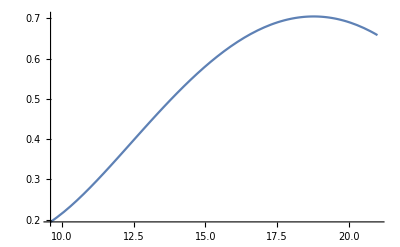

```mathematica
e=1/1000;
Plot[{(ⅇ^(-a/12) (a^2-a (3+e)+12 π^2))/π^2-8 (1+e)^2  (1+ⅇ^(-9.6/2))},{a,9.6,21}]
Clear[e]
```

```mathematica
D[(ⅇ^(-a/12) (a^2-a (3+e)+12 π^2))/π^2,a]//Simplify
D[(ⅇ^(-a/12) (a^2-a (3+e)+12 π^2))/π^2,a,a]//Simplify
```

(ⅇ^(-a/12) (-a^2+a (27+e)-12 (3+e+π^2)))/(12 π^2)

(ⅇ^(-a/12) (a^2-a (51+e)+12 (30+2 e+π^2)))/(144 π^2)

We can see the sign of the first derivative depends only on (a^2-a (3+e)+12 π^2), which is concave. Thus, it suffices to check that it is positive at a=9.6,17.
The sign of the second derivative depends only on a^2-a (51+e)+12 (30+2 e+π^2), which is convex. Thus, to check it’s negative, we only need to check at a=17, 21. 
based on these checks, the quantity is either increasing or concave on all of [9.6,21], and so it has no local minima. Thus, we may check it’s positivity at simply 9.6,21

```mathematica
(a^2-a (3+e)+12 π^2)/.{a->9.6,e->1/1000}
(a^2-a (3+e)+12 π^2)/.{a->17,e->1/1000}
a^2-a (51+e)+12 (30+2 e+π^2)/.{a->17.,e->1/1000}
a^2-a (51+e)+12 (30+2 e+π^2)/.{a->21.,e->1/1000}
(ⅇ^(-a/12) (a^2-a (3+e)+12 π^2))/π^2-8 (1+e)^2  (1+ⅇ^(-9.6/2))/.{a->9.6,e->1/1000}
(ⅇ^(-a/12) (a^2-a (3+e)+12 π^2))/π^2-8 (1+e)^2  (1+ⅇ^(-9.6/2))/.{a->21.,e->1/1000}
```

181.786

237983/1000+12 π^2

-99.5577

-151.562

0.194095

0.658379

and those calculations all work out as desired. So A<C

#### B<C:

We have the partial of F w . r . t t2 @ (-1, 1), call it B and an upper bound B1

```mathematica
B1=f1[0,-1,1]f2[1,1,1]-f1[0,1,-1]f2[1,-1,-1]//Simplify
```

(3 a ⅇ^(-3 a/4) (2-3 a+2 (1+e) ⅇ^(a/2)))/(2 π^2)

```mathematica
C0 2Pi^2Exp[a/4]/a//Simplify
B1 2Pi^2Exp[a/4]/a
```

2 (-3+a-e) ⅇ^(-a/12)

3 ⅇ^(-a/2) (2-3 a+2 (1+e) ⅇ^(a/2))

```mathematica
D[2 (-3+a-e) ⅇ^(-a/12),a,a]//Simplify
```

1/72 (-27+a-e) ⅇ^(-a/12)

so the second quantity is concave as claimed for a<=21. 
Now since  3 ((2-3 a)ⅇ^(-a/2) +2 (1+e))<=3 ((2-3 a)ⅇ^(-9.6/2) +2 (1+e))for a>=9.6
and 
3 ((2-3 a)ⅇ^(-a/2) +2 (1+e))<=3 ((2-3 a)ⅇ^(-11/2) +2 (1+e))for a>=11, with the latter terms linear in a, it suffices to show 
2 (-3+a-e) ⅇ^(-a/12)-3 ((2-3 a)ⅇ^(-9.6/2) +2 (1+e))>=0 at a=9.6
and 
2 (-3+a-e) ⅇ^(-a/12)-3 ((2-3 a)ⅇ^(-11/2) +2 (1+e))>=0 
at a=11,21 (which implies the previous inequality holds at a=11 as well)

```mathematica
2 (-3+a-e) ⅇ^(-a/12)-3 ((2-3 a)ⅇ^(-9.6/2) +2 (1+e))/.{a->9.6,e->1/1000}
2 (-3+a-e) ⅇ^(-a/12)-3 ((2-3 a)ⅇ^(-11/2) +2 (1+e)) /.{a->11.,e->1/1000}
2 (-3+a-e) ⅇ^(-a/12)-3 ((2-3 a)ⅇ^(-11/2) +2 (1+e)) /.{a->21.,e->1/1000}
```

0.585915

0.770865

0.997394

and those all work as desired .

## 4 Points: Large A

### Comparison of t1 and t2 derivatives of F at (-1,1)

```mathematica
N[3 *21 Exp[-21/2](1+e)/.e->1/1000]
N[99/10000]
```

0.00173653

0.0099

### (F-G)(-1,1/2)>=0

```mathematica
Clear[a] 
N[3Exp[-a/12]-2(1+e)^3+3a(2-4e)/(2Pi^2)/.{a->21,e->1/1000,e2->1/100}]
N[D[3Exp[-a/12]-2(1+e)^3+3a(2-4e)/(2Pi^2),a]/.{a->21,e->1/1000,e2->1/100}]
```

4.88578

0.259912

### Linearization portion for the region [-1,Cos[2Pi Sqrt[3]/4]x[1/2,1]

#### some initialization if you want to play with things, not necessary.

Here are some functions to initialize if you want to play around with how our bounds for g_a,b compare to the “actual” (and by actual i mean a very, very, very, precise approximation) g and how Flow2 compares to the “actual” F. Run this cell block, then you can add Glin, Gest2, or Fest to any of the plots to see how they compare.

```mathematica
const[c_,w_]:=w(thetaderivm1[c,2]thetaestt2[3c,1,2]-thetaderiv1[c,2]thetaestt2[3c,-1,2])+(1-w)(thetaderiv1[3c,2]thetaestt2[c,-1,2]-thetaderivm1[3c,2]thetaestt2[c,1,2]);
Clear[d,x,k,t1,t2]
thetaest2[c_,x_,k_]:=Sum[Exp[-c(n+x)^2],{n,-k,k}]
thetaestt2[c_,t_,k_]:=thetaest2[c,ArcCos[t]/(2Pi),k]
thetaderiv1[c_,k_]:=c/(2Pi^2)Sum[(1-2c n^2)Exp[-c n^2],{n,-k,k}]
thetaderivm1[c_,k_]:=c/(2Pi^2)Sum[(2c(n-1/2)^2-1)Exp[-c(n-1/2)^2],{n,-k,k}]
thetaderiv1s[c_,k_]:=Sum[(1-2c n^2)Exp[-c n^2],{n,-k,k}]
thetaderivm1s[c_,k_]:=Sum[(2c(n-1/2)^2-1)Exp[-c(n-1/2)^2],{n,-k,k}]
Fest[c_,t1_,t2_]:=thetaestt2[c,t1,3]thetaestt2[3c,t2,3]+thetaestt2[c,-t1,3]thetaestt2[3c,-t2,3];
Gest[c_,t1_,t2_]:=Fest[c,-1,1]+(t1* t2+t2^2)(thetaderivm1[c,2]thetaestt2[3c,1,2]-thetaderiv1[c,2]thetaestt2[3c,-1,2])
Ft1derivest[c_,u_]:=Exp[-c/4]Exp[-3c u^2]c/(Pi^2)((c/2-1)-Exp[-c/2]/2(Exp[3c u+Exp[-3c u]]))
Gt1derivest[c_,u_]:=Cos[2Pi u](3c/(2Pi^2)(2Exp[-c/4]-(3c-1)Exp[-3c/4]))
Gest2[c_,t1_,t2_]:=Fest[c,-1,1]+(t1* t2+t2^2)(thetaestt2[c,-1,2]thetaderiv1[3c,2]-thetaderivm1[3c,2]thetaestt2[c,1,2])
Fterm1[c_,x_,u_,n_,m_]:=Exp[-c(n+x)^2]Exp[-3c(m+u)^2]
Fterm2[c_,x_,u_,n_,m_]:=Exp[-c(n+1/2-x)^2]Exp[-3c(m+1/2-u)^2]
Gest3[c_,t1_,t2_,w_]:=w Gest[c,t1,t2]+(1-w)Gest2[c,t1,t2]
Clear[c]
const[c_,w_]:=w(thetaderivm1[c,2]thetaestt2[3c,1,2]-thetaderiv1[c,2]thetaestt2[3c,-1,2])+(1-w)(thetaestt2[c,-1,2]thetaderiv1[3c,2]-thetaderivm1[3c,2]thetaestt2[c,1,2])
Glin[c_,w_,t1_,t2_,a_,b_]:=Fest[c,-1,1]+const[c,w](t2^2 +b t1+ a t2-a b)
```

#### the meat

Here is our lower bound for F, Flow2. (Flow1 is used in the 6 point problem and is too crude for approximating the 4-point F, though it is a lower bound).

```mathematica
Flow2[a_,x_,u_]:=(Exp[-a x^2]+Exp[-a(x-1)^2])Exp[-3a u^2]+Exp[-a(1/2-x)^2]Exp[-3a (1/2-u)^2]
```

It is straightforward to compute g_{c,b}=F(-1,1)+ell t2(t_2+c) +b ell t_1- b c ell. Thus, we obtain the upper for g_{c,b} when t1,b<0, t2,c in [1/2,1]

```mathematica
Clear[a,glinbound,b,c]
ell[-1] =(2-4e) 3a Exp[-a/4]/(2Pi^2);
ell[1] = (1 + e)3 a Exp[-a/4]/(Pi^2);
glinbound[b_, c_, t1_, t2_] := 2 (1 + e)^3 Exp[-a/4] + ell[-1] t2 (t2 +b) + ell[-1]*c *t1  - b*c ell[1];
Clear[a]
```

Side observation for when we do this more rigorously: Notice the glinbound is increasing in t1, so i can even overestimate t1 on a vertical segment if i only want to work with rational t2’s. Note also that Flow2 is increasing in t2 so on a horizontal segment, i can underestimate t2 if I want to only work with rational u’s.

We first want to show that g_{-1,1} is greater than F on the set {(cos[2Pi Sqrt[3]/4],t2) for t2 in (.7,1)} and {(t1, .7), for t1 in (-1,Cos[2Pi Sqrt[3]/4])} . We do so by comparing the respective upper and lower bounds on these segments.

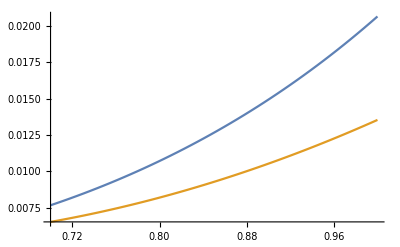

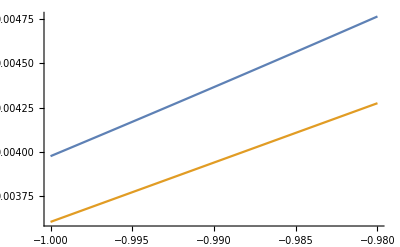

```mathematica
a=21;
t1=Cos[2Pi Sqrt[3]/4];
Plot[{Flow2[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound[-1,1,t1,t2]/.{e->1/1000,e2->1/100}},{t2,.7,1}]
Clear[t1]
t2=.7;
Plot[{Flow2[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound[-1,1,t1,t2]/.{e->1/1000,e2->1/100}},{t1,-1,-.98}]
Clear[a,t2]
```

Next, we want to show that g_ {-1, .7} is greater than F on the set {(cos[2 Pi Sqrt[3]/4], t2) for t2 in (.6, .7)} and {(t1, .6), for t1 in (-1, Cos[2 Pi Sqrt[3]/4])} .

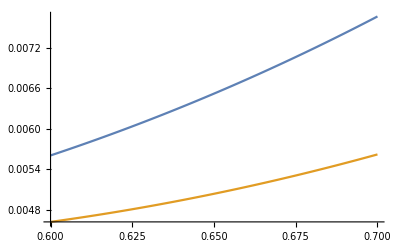

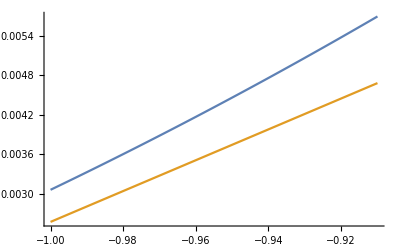

```mathematica
a=21;
t1=Cos[2Pi Sqrt[3]/4];
Plot[{Flow2[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound[-1,.7,t1,t2]/.{e->1/1000,e2->1/100}},{t2,.6,.7}]
Clear[t1]
t2=.6;
Plot[{Flow2[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound[-1,.7,t1,t2]/.{e->1/1000,e2->1/100}},{t1,-1,-.91}]
Clear[a,t2]
```

We have to do this one more time and show that g_ {-1, .6} is greater than F on the set {(cos[2 Pi Sqrt[3]/4], t2) for t2 in (.5, .6)} and {(t1, .5), for t1 in (-1, Cos[2 Pi Sqrt[3]/4])} .

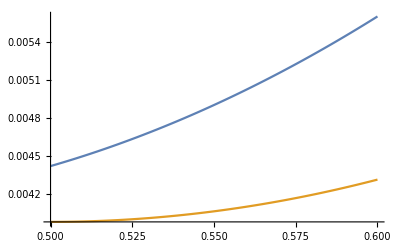

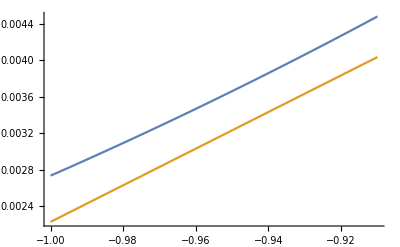

```mathematica
a=21;
t1=Cos[2Pi Sqrt[3]/4];
Plot[{Flow2[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound[-1,.6,t1,t2]/.{e->1/1000,e2->1/100}},{t2,.5,.6}]
Clear[t1]
t2=1/2;
Plot[{Flow2[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound[-1,.6,t1,t2]/.{e->1/1000,e2->1/100}},{t1,-1,-.91}]
Clear[t2]
```

It remains to show that these differences, when multiplied by a factor of Exp[a/4] are growing in a when a = 21. Then since the bound for g is linear in a, we can just invoke convexity of the bound of F in a and be done. These checks are not nearly so delicate.

```mathematica
Clear[a]
DFlow2[x_,u_]:=D[Exp[a/4]Flow2[a,x,u],a]/.a->21
Dglinbound[b_,c_,t1_,t2_]:=D[Exp[a/4]glinbound[b,c,t1,t2],a]/.a->21
```

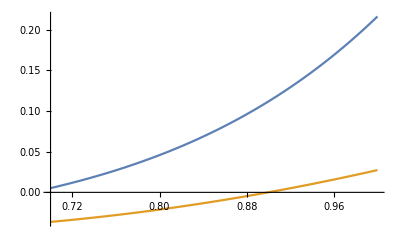

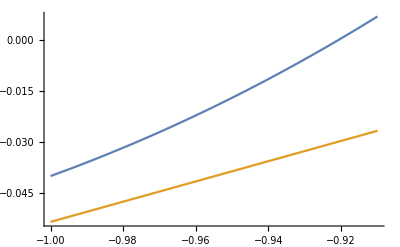

```mathematica
t1=Cos[2Pi Sqrt[3]/4];
Plot[{DFlow2[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound[-1,1,t1,t2]/.{e->1/1000,e2->1/100}},{t2,.7,1}]
Clear[t1]
t2=.7;
Plot[{DFlow2[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound[-1,1,t1,t2]/.{e->1/100,e2->1/1000}},{t1,-1,-.91}]
Clear[t2]
```

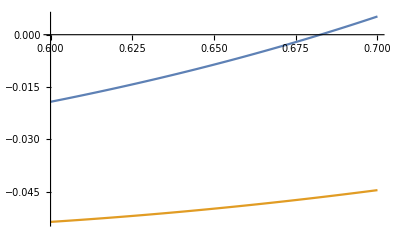

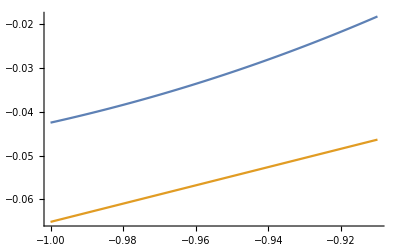

```mathematica
t1=Cos[2Pi Sqrt[3]/4];
Plot[{DFlow2[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound[-1,.7,t1,t2]/.{e->1/1000,e2->1/100}},{t2,.6,.7}]
Clear[t1]
t2=.6;
Plot[{DFlow2[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound[-1,.7,t1,t2]/.{e->1/100,e2->1/1000}},{t1,-1,-.91}]
Clear[t2]
```

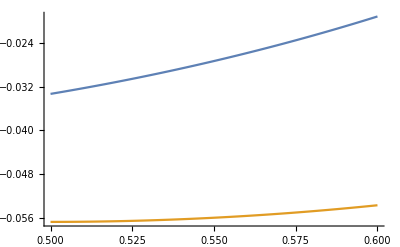

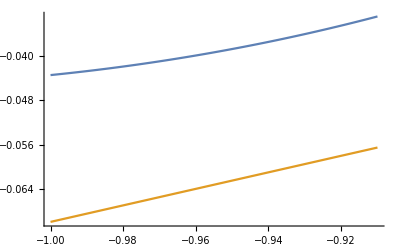

```mathematica
t1=Cos[2Pi Sqrt[3]/4];
Plot[{DFlow2[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound[-1,.7,t1,t2]/.{e->1/1000,e2->1/100}},{t2,.5,.6}]
Clear[t1]
t2=.5;
Plot[{DFlow2[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound[-1,.5,t1,t2]/.{e->1/100,e2->1/1000}},{t1,-1,-.91}]
Clear[t2]
```

### d(F-G)/dt_1, d^2(F-G)/dt_1dt_2>=0 at p*

First, we handle the first derivative inequality. 

There were a couple of random inequalities needed to clean up the final bounds. Both of the first two quantities below are clearly monotone in a, so just check at a=21 that they satisfy the bound claimed in the text!

```mathematica
x=Sqrt[3]/4;
u=Sqrt[3]/12;
N[x-(1-x)Exp[-a(1-2x)]/.a->21]
N[(1/2-x)2(1+e)Exp[-a(1-x-3u)]/.{a->21,e->1000}]
N[Sin[2Pi x]]
N[Cos[2Pi u]]
Clear[x,u]
```

0.398995

8.04607

0.408576

0.616191

All that' s left is to check that final quantity...

```mathematica
38/41-3(1+e).62/Pi/.e->1/1000
```

0.334181

Now onto the mixed partial inequality.
The first quantity is monotone in a again so just check at a=21

We have a couple more one off inequalities to verify for the mixed partial part of the proof

```mathematica
x=Sqrt[3]/4;
u=Sqrt[3]/12;
N[u-(1-u)Exp[-3a(1-2u)]]/.a->21
N[Sin[2Pi u]]
Clear[x,u]
```

0.144338

0.787597

All that' s left to do is to check the final quantity is positive at a=21...

```mathematica
14*5*3*39*a/(100*4*41)-3(1+e)/.{e->1/1000,a->21}
```

76713/10250

## 6 Points: Large A

### Coefficient Bounds:

-1 as an argument will yield lower bounds, 1 for upper bound. Run this section to get all the bounds

These computations give the a01 bounds

```mathematica
a01[-1]=f1[0,1,-1]f2[1,-1/2,-1];
a01[1]=f1[0,1,1]f2[1,-1/2,1];
```

These computations give the a10 bounds

```mathematica
b=-1;
(f1[0,1,b]f2[0,-1/2,b]-f1[0,-1,-b]f2[0,1/2,-b])/2+a01[b]/2
b=1;
(f1[0,1,b]f2[0,-1/2,b]-f1[0,-1,-b]f2[0,1/2,-b])/2+a01[b]/2
Clear[b]
```

1/2 (ⅇ^(-a/3)-2 (1+e)^2 ⅇ^(-a/3))+(a (1-e) ⅇ^(-a/3))/(√3 π)

1/2 (-2 ⅇ^(-a/3)+(1+e)^2 ⅇ^(-a/3))+(a (1+e) ⅇ^(-a/3))/(√3 π)

Since (1 + e)^2 < 1 + 3 e, we obtain

```mathematica
a10[-1]=(-1-6e) ⅇ^(-a/3)/2+(a (1-e) ⅇ^(-a/3))/(√3 π);
a10[1]=(-1+3e) ⅇ^(-a/3)/2+(a (1+e) ⅇ^(-a/3))/(√3 π);
```

The next computations produce the bounds for a00, again using the fact that (1 + e)^2 < 1 + 3 e.

```mathematica
b=-1;
a00[-1]=(f1[0,1,b]f2[0,-1/2,b]+f1[0,-1,b]f2[0,1/2,b])/2
b=1;
(f1[0,1,b]f2[0,-1/2,b]+f1[0,-1,b]f2[0,1/2,b])/2
a00[1]=3/2 (1+3e) ⅇ^(-a/3)
```

(3 ⅇ^(-a/3))/2

3/2 (1+e)^2 ⅇ^(-a/3)

3/2 (1+3 e) ⅇ^(-a/3)

Next, we compute a02 bound with the formula a02 = 4/9 f1 (-1) (f2 (-1) - f2 (1/2) + 3/2 f2' (1/2)) . For the lower bound, we throw away the f2 (-1), for the upper bound, we bound f1 (-1) f2 (-1) by Exp[-a/3] *e2 (corresponding to epsilon_2 in the text) .

```mathematica
a02[-1]=4/9f1[0,-1,-1](-f2[0,1/2,1]+3/2f2[1,1/2,-1])
a02[1]=4/9f1[0,-1,1](-f2[0,1/2,-1]+3/2f2[1,1/2,1])+e2 Exp[-a/3]
```

8/9 ⅇ^(-a/4) (-((1+e) ⅇ^(-a/12))+(√3 a (1-e) ⅇ^(-a/12))/(2 π))

ⅇ^(-a/3) e2+8/9 (1+e) ⅇ^(-a/4) (-ⅇ^(-a/12)+(√3 a ⅇ^(-a/12))/(2 π))

Finally, we compute the b00 bound by using the formula 
b00 = a00 + a02/4

```mathematica
b00[-1]=a02[-1]/4+a00[-1]
b00[1]=a02[1]/4+a00[1]
```

(3 ⅇ^(-a/3))/2+2/9 ⅇ^(-a/4) (-((1+e) ⅇ^(-a/12))+(√3 a (1-e) ⅇ^(-a/12))/(2 π))

3/2 (1+3 e) ⅇ^(-a/3)+1/4 (ⅇ^(-a/3) e2+8/9 (1+e) ⅇ^(-a/4) (-ⅇ^(-a/12)+(√3 a ⅇ^(-a/12))/(2 π)))

```mathematica
a00[-1]Exp[a/3]
a00[1]Exp[a/3]
a01[-1]Exp[a/3]
a01[1]Exp[a/3]
a10[-1]Exp[a/3]
a10[1]Exp[a/3]
a02[-1]Exp[a/3]
a02[1]Exp[a/3]
b00[-1]Exp[a/3]
b00[1]Exp[a/3]
```

3/2

3/2 (1+3 e)

(2 a (1-e))/(√3 π)

(2 a (1+e))/(√3 π)

ⅇ^(a/3) (1/2 (-1-6 e) ⅇ^(-a/3)+(a (1-e) ⅇ^(-a/3))/(√3 π))

ⅇ^(a/3) (1/2 (-1+3 e) ⅇ^(-a/3)+(a (1+e) ⅇ^(-a/3))/(√3 π))

8/9 ⅇ^(a/12) (-((1+e) ⅇ^(-a/12))+(√3 a (1-e) ⅇ^(-a/12))/(2 π))

ⅇ^(a/3) (ⅇ^(-a/3) e2+8/9 (1+e) ⅇ^(-a/4) (-ⅇ^(-a/12)+(√3 a ⅇ^(-a/12))/(2 π)))

ⅇ^(a/3) ((3 ⅇ^(-a/3))/2+2/9 ⅇ^(-a/4) (-((1+e) ⅇ^(-a/12))+(√3 a (1-e) ⅇ^(-a/12))/(2 π)))

ⅇ^(a/3) (3/2 (1+3 e) ⅇ^(-a/3)+1/4 (ⅇ^(-a/3) e2+8/9 (1+e) ⅇ^(-a/4) (-ⅇ^(-a/12)+(√3 a ⅇ^(-a/12))/(2 π))))

### Necessary Derivative Conditions

#### t1 derivative at (-1,1)

it suffices to show the t1 deriv of g at (-1, 1) is negative . it equals a10 - a02 and up to a factor of Exp[a/3], is linear in a. So show it’s negative at a=9.6 with negative coefficient of a.

```mathematica
Exp[a/3](a10[1]-a02[-1])//Simplify
Exp[a/3](a10[1]-a02[-1])/.{a->9.6,e->1/1000}
```

(2 √3 a (-1+7 e)+(7+43 e) π)/(18 π)

-0.19269

#### t1 derivative at (-1, 1/2)

Bound below f1' (-1) f2 (1/2) - a10 - a02/2. Similar to before, the factor of Exp[a/3] makes it quadratic in a, so just check coefficient of a^2, value and derivative at a=9.6

```mathematica
Exp[a/3](f1[1,-1,-1]f2[0,1/2,-1]-a10[1]-a02[1]/2)//Simplify
D[Exp[a/3](f1[1,-1,-1]f2[0,1/2,-1]-a10[1]-a02[1]/2),a]/.{a-> 9.6,e->1/1000,e2->1/100}
Exp[a/3](f1[1,-1,-1]f2[0,1/2,-1]-a10[1]+a02[1]/2)/.{a-> 9.6,e->1/1000,e2->1/100}
```

(9 a^2+(17-19 e-9 e2) π^2-2 a (9+5 √3 (1+e) π))/(18 π^2)

0.564762

3.16614

#### t1 derivative at (1, -1/2)

Bound above f1' (1) f2 (-1/2) - a10 + a02/2. Similar to before, the factor of Exp[a/3] makes it linear in a, so just check coefficient of a and value at a = 9.6

```mathematica
f1[1,1,1]f2[0,-1/2,1]//Simplify
-a10[-1]+a02[1]/2//Simplify
Exp[a/3](f1[1,1,1]f2[0,-1/2,1]-a10[-1]+a02[1]/2)/.{a->9.6,e->1/1000,e2->1/100}
D[Exp[a/3](f1[1,1,1]f2[0,-1/2,1]-a10[-1]+a02[1]/2),a]/.{a->9.6,e->1/1000,e2->1/100}//Simplify
```

(a (1+e) ⅇ^(-a/3))/(2 π^2)

(ⅇ^(-a/3) (2 √3 a (-1+5 e)+(1+46 e+9 e2) π))/(18 π)

-0.0352046

-0.0102412

### Linearization Portion of the proof

For the 6 point linearization portion of the proof, we can utilize the two term lower bound for F. Below is an upper bound for G_{b,c}, and hence for G when t1>=b, t2<=c, in the case that t1<=0, t2>=0 (so t1t2<=0).

```mathematica
Flow1[a_,x_,u_]:=(Exp[-a x^2]+Exp[-a(x-1)^2])Exp[-3a u^2]
Clear[a,glinbound2,b,c,t1,t2]
glinbound2[b_,c_,t1_,t2_]:=b00[1]+a10[-1]t1+ a01[1]t2+a02[1]t2^2+a02[-1](c t1 +b t2- b c);
Clear[a]
```

We first want to show that g_ {-1, 1/2} is greater than F on the set {(-Sqrt[2]/2, t2) for t2 in [1/4, 1/2]} and {(t1, 1/4), for t1 in [-1,-Sqrt[2]/2]}  when a=9.6.

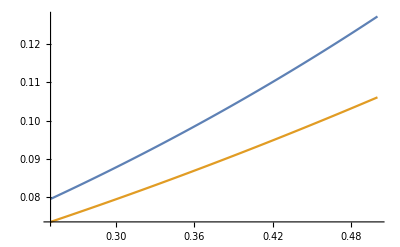

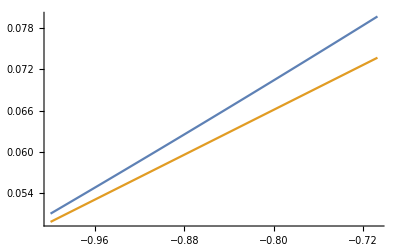

```mathematica
a=9.6;
t1=Cos[2Pi*3/8];
b=-1;
c=1/2;
Plot[{Flow1[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t2,1/4,c}]
Clear[t1]
t2=1/4;
Plot[{Flow1[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t1,b,Cos[2Pi *3/8]}]
Clear[a,b,c,t2]
```

Next, we move to show that g_ {-1, 1/4} is greater than F on the set {(-Sqrt[2]/2, t2) for t2 in [0, 1/4]} and {(t1, 0), for t1 in [-1, -Sqrt[2]/2]}  when a = 9.6 .

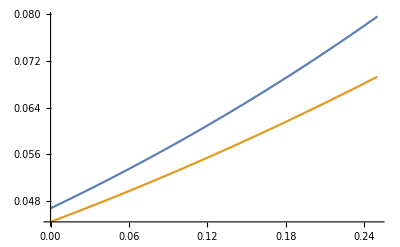

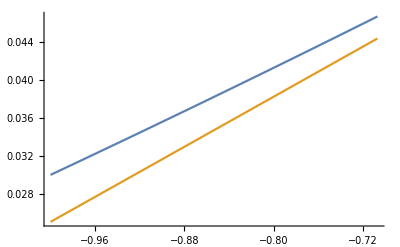

```mathematica
a=9.6;
t1=Cos[2Pi*3/8];
b=-1;
c=1/4;
Plot[{Flow1[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t2,0,c}]
Clear[t1]
t2=0;
Plot[{Flow1[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t1,b,Cos[2Pi *3/8]}]
Clear[a,b,c,t2]
```

Below is an upper bound for G_ {b, c}, and hence for G when t1 >= b, t2 <= c, in the case that t1 <= 0, t2 <= 0 (so t1t2 >= 0) .

```mathematica
Clear[a,glinbound2,b,c,t1,t2]
glinbound2[b_,c_,t1_,t2_]:=b00[1]+a10[-1]t1+ a01[-1]t2+a02[1]t2^2+a02[1](c t1 +b t2- b c);
Clear[a,b,c,t2]
```

We want to show that g_ {-Sqrt[2]/2, 0} is greater than F on the set {(-sqrt[2]/2, t2) for t2 in [-1/10, 0]}, {(0, t2) for t2 in [-1/10, 0]} and {(t1, -1/10), for t1 in [ -Sqrt[2]/2,0]}  when a = 9.6 .

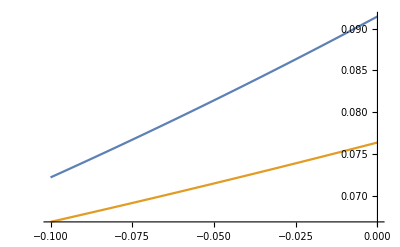

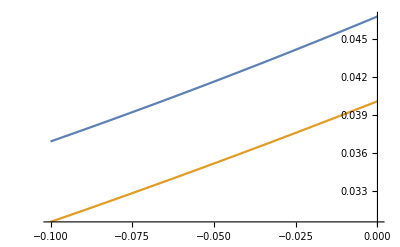

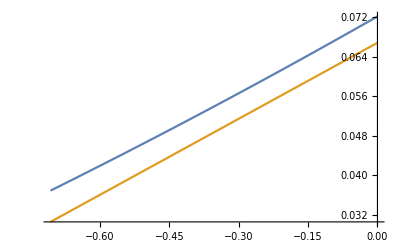

```mathematica
a=9.6;
t1=0;
b=-Sqrt[2]/2;
c=0;
Plot[{Flow1[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t2,-1/10,c}]
Clear[t1]
t1=-Sqrt[2]/2;
Plot[{Flow1[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t2,-1/10,c}]
Clear[t1]
t2=-1/10;
Plot[{Flow1[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t1,b,0}]
Clear[a,b,c,t2]
```

We last want to show that g_ {-Sqrt[2]/2, -1/10} is greater than F on the set {(-sqrt[2]/2, t2) for t2 in [-1/5, -1/10]}, {(0, t2) for t2 in [-1/5, -1/10]} and {(t1, -1/5), for t1 in [ -Sqrt[2]/2, 0]}  when a = 9.6 .

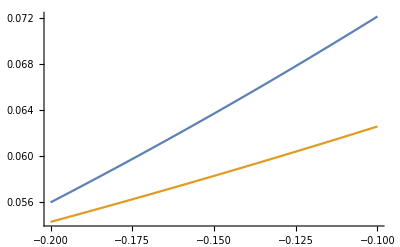

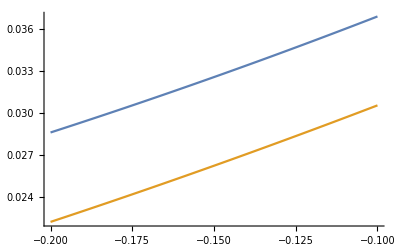

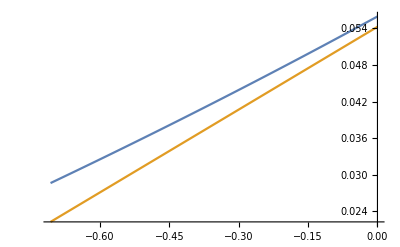

```mathematica
a=9.6;
t1=0;
b=-Sqrt[2]/2;
c=-1/10;
Plot[{Flow1[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t2,-1/5,c}]
Clear[t1]
t1=-Sqrt[2]/2;
Plot[{Flow1[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t2,-1/5,c}]
Clear[t1]
t2=-1/5;
Plot[{Flow1[a,ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],glinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t1,b,0}]
Clear[a,b,c,t2]
```

Side note: If you want to see how our upper bound for g_ {a, b} compares to the actual interpolant, the below function g8 is a very, very precise approximation of the interpolant, so you can add it to any of the plots.

```mathematica
Clear[a,t1,t2]
alpha[t1_,t2_]:=t2(t1+t2)+1/4
Fest6[c_,t1_,t2_]:=thetaestt2[c,t1,4]thetaestt2[3c,t2,4]
c01[a_]:=D[Fest6[a,1,t],t]/.t->-1/2
c00[a_]:=(Fest6[a,1,-1/2]+Fest6[a,-1,1/2])/2
c10[a_]:=((D[Fest6[a,1,t],t]/.t->-1/2)+Fest6[a,1,-1/2]-Fest6[a,-1,1/2])/2
c02[a_]:=4/9(Fest6[a,-1,-1]-c00[a]+c01[a]+c10[a]);
g8[a_,t1_,t2_]:=c00[a]+t1 c10[a]+t2 c01[a]+c02[a]alpha[t1,t2]
```

It remains to show that these differences, when multiplied by a factor of Exp[a/3] are growing in a when a =9.6. Then since the bound for g is linear in a, we can just invoke convexity of the bound of F in a and be done . These checks are not nearly so delicate .

```mathematica
Clear[a]
DFlow1[x_,u_]:=D[Exp[a/3]Flow2[a,x,u],a]/.a->9.6
Dglinbound2[b_,c_,t1_,t2_]:=D[Exp[a/3]glinbound2[b,c,t1,t2],a]/.a->9.6
```

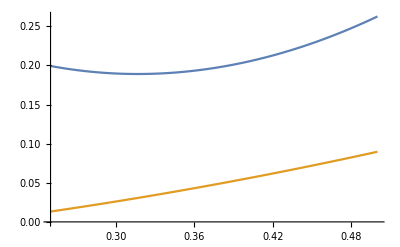

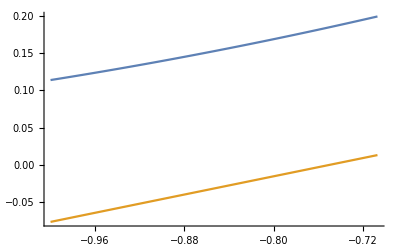

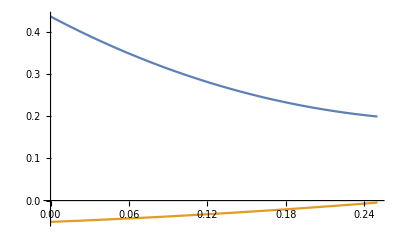

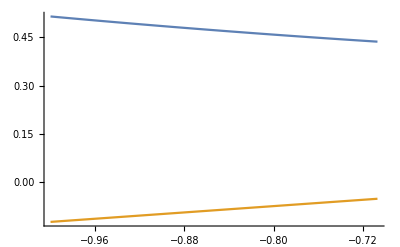

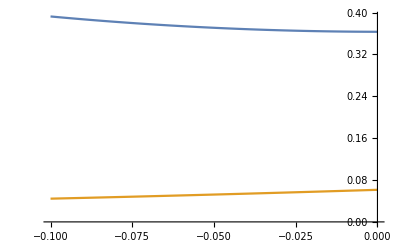

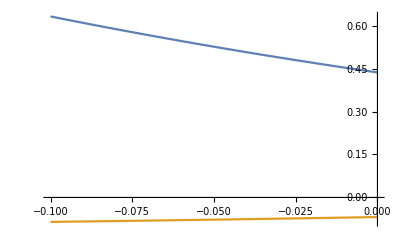

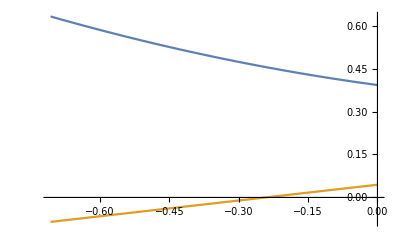

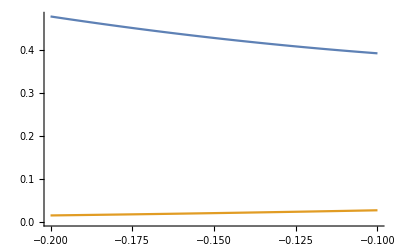

```mathematica
t1=Cos[2Pi*3/8];
b=-1;
c=1/2;
Plot[{DFlow1[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t2,1/4,c}]
Clear[t1]
t2=1/4;
Plot[{DFlow1[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t1,b,Cos[2Pi *3/8]}]

t1=Cos[2Pi*3/8];
b=-1;
c=1/4;
Plot[{DFlow1[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t2,0,c}]
Clear[t1]
t2=0;
Plot[{DFlow1[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t1,b,Cos[2Pi *3/8]}]
Clear[a,b,c,t2]

Clear[a,glinbound2,b,c,t1,t2]
glinbound2[b_,c_,t1_,t2_]:=b00[1]+a10[-1]t1+ a01[-1]t2+a02[1]t2^2+a02[1](c t1 +b t2- b c);
Clear[a,b,c,t2]
Clear[a]
DFlow1[x_,u_]:=D[Exp[a/3]Flow2[a,x,u],a]/.a->9.6
Dglinbound2[b_,c_,t1_,t2_]:=D[Exp[a/3]glinbound2[b,c,t1,t2],a]/.a->9.6

t1=0;
b=-Sqrt[2]/2;
c=0;
Plot[{DFlow1[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t2,-1/10,c}]
Clear[t1]
t1=-Sqrt[2]/2;
Plot[{DFlow1[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t2,-1/10,c}]
Clear[t1]
t2=-1/10;
Plot[{DFlow1[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t1,b,0}]
Clear[a,b,c,t2]

t1=0;
b=-Sqrt[2]/2;
c=-1/10;
Plot[{DFlow1[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t2,-1/5,c}]
Clear[t1]
t1=-Sqrt[2]/2;
Plot[{DFlow1[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t2,-1/5,c}]
Clear[t1]
t2=-1/5;
Plot[{DFlow1[ArcCos[t1]/(2Pi),ArcCos[t2]/(2Pi)],Dglinbound2[b,c,t1,t2]/.{e->1/1000,e2->1/100}},{t1,b,0}]
Clear[a,b,c,t2]
```

and that' s that .

### t1 derivative of the difference at (-Sqrt[2]/2,0)

we' ve got a lower bound for the t1 deriv of F at (-Sqrt[2]/2, 0), meanwhile the t1 deriv of G at (-Sqrt[2]/2, 0) is a10

```mathematica
-(3/8)^2-3(1/4)^2+1/3
```

1/192

```mathematica
Sqrt[2]a Exp[a/192](3-5Exp[-a/4])/(8Pi)
Exp[a/3]a10[1]
```

(a ⅇ^(a/192) (3-5 ⅇ^(-a/4)))/(4 √2 π)

ⅇ^(a/3) (1/2 (-1+3 e) ⅇ^(-a/3)+(a (1+e) ⅇ^(-a/3))/(√3 π))

check that the t1 deriv (times Exp[a/3]) is larger at a = 9.6.

```mathematica
Sqrt[2]a Exp[a/192](3-5Exp[-a/4])/(8Pi)-Exp[a/3]a10[1]/.{a->9.6,e->1/1000}
```

0.178554

Now we claim the above quantity is increasing in a. The deriv of the G term with respect to a is constant.

```mathematica
D[Sqrt[2]a Exp[a/192](3-5Exp[-a/4])/(8Pi),a]//Simplify
D[Exp[a/3]a10[1],a]//Simplify
```

(ⅇ^(-47 a/192) (-960+235 a+576 ⅇ^(a/4)+3 a ⅇ^(a/4)))/(768 √2 π)

(1+e)/(√3 π)

We drop the - 960 + 235 a term which is positive for a >= 9.6. The resulting quantity is increasing in a, so we simply evaluate at a=9.6 and see it’s larger than (e+1)/(√3 π)

```mathematica
(ⅇ^(-47 a/192) (576 ⅇ^(a/4)+3 a ⅇ^(a/4)))/(768 √2 π)//Expand
(ⅇ^(-47 a/192) (576 ⅇ^(a/4)+3 a ⅇ^(a/4)))/(768 √2 π)/.a->9.6
N[(1+e)/(√3 π)/.e->1/1000]
```

(3 ⅇ^(a/192))/(4 √2 π)+(a ⅇ^(a/192))/(256 √2 π)

0.186338

0.18396

### Positivity of L1

```mathematica
b=-1;
f1[0,-1,b]f2[0,1/2,b]-f1[0,1,-b]f2[0,-1/2,-b]//Simplify
b=1;
f1[0,-1,b]f2[0,1/2,b]-f1[0,1,-b]f2[0,-1/2,-b]//Simplify
Clear[b]
```

-((-1+2 e+e^2) ⅇ^(-a/3))

(1+4 e+2 e^2) ⅇ^(-a/3)

This along with the fact that e^2 < e yields the first inequalities on (1-3epsilon)Exp[-a/3]<=f1 (-1) f2 (1/2) - f1 (1) f2 (-1/2) <=(1+6e)Exp[-a/3] (we also already did this in computing bound of a10)

checking that a10[-1] - a02[1]/2 is positive ...

```mathematica
a10[-1]-a02[1]/2 //Simplify
a10[-1]-a02[1]/2 /.{a->9.6,e->1/1000,e2->1/100}
```

(ⅇ^(-a/3) (2 √3 a (1-5 e)-(1+46 e+9 e2) π))/(18 π)

0.0212792

Now when t1 = 1, we have the upper bound on (f1(-1) f2 (1/2) - f1 (1) f2 (-1/2)+a02)/(a10+a02 t2)
given below, which we claim is decreasing in a:

```mathematica
Clear[t2]
```

```mathematica
(1+6e+Exp[a/3]a02[1])/(Exp[a/3](a10[-1]+t2 a02[1]))
D[(1+6e+Exp[a/3]a02[1])/(Exp[a/3](a10[-1]+t2 a02[1])),a]//Simplify
```

(ⅇ^(-a/3) (1+6 e+ⅇ^(a/3) (ⅇ^(-a/3) e2+8/9 (1+e) ⅇ^(-a/4) (-ⅇ^(-a/12)+(√3 a ⅇ^(-a/12))/(2 π)))))/(1/2 (-1-6 e) ⅇ^(-a/3)+(a (1-e) ⅇ^(-a/3))/(√3 π)+(ⅇ^(-a/3) e2+8/9 (1+e) ⅇ^(-a/4) (-ⅇ^(-a/12)+(√3 a ⅇ^(-a/12))/(2 π))) t2)

-(12 √3 π (7+9 e2+12 t2+2 e^2 (-5+36 t2)+e (87-9 e2+84 t2)))/(-2 √3 a (3+4 t2+e (-3+4 t2))+π (9+16 t2-18 e2 t2+2 e (27+8 t2)))^2

Indeed, the sign of its derivative depends only on (7+9 e2+12 t2+2 e^2 (-5+36 t2)+e (87-9 e2+84 t2)) , which is increasing in t2 and positive at t2=-1/2, as desired.

```mathematica
7+9 e2+12 t2+2 e^2 (-5+36 t2)+e (87-9 e2+84 t2)/.{e->1/1000,t2->-1/2,e2->1/100}
```

70929/62500

In sum then, L (1, t2) >= 0 when t2 in [-1/2, 0] if the following lower bound is positive for a=9.6

```mathematica
3u(1-e)2Pi/((1+e)Sin[2Pi u])-2-(1+6e+Exp[a/3]a02[1])/(Exp[a/3](a10[-1]+t2 a02[1]))/.{a->96/100,e->1/1000,e2->1/100}//Simplify
```

(-197950 π (1+2 t2)+48 √3 (4999+4004 t2))/(-24 √3 (2997+4004 t2)+25 π (4527+7918 t2))+(2997 ArcCos[t2])/(1001 √(1-t2^2))

ArcCos[t2]/(2 π)

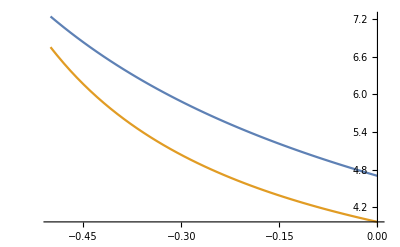

```mathematica
u=ArcCos[t2]/(2Pi)
Plot[{3u(1-e)2Pi/((1+e)Sin[2Pi u])/.{e->1/1000},2+(1+6e+Exp[a/3]a02[1])/(Exp[a/3](a10[-1]+t2 a02[1]))/.{a->9.6,e->1/1000,e2->1/100}},{t2,-1/2,0}]
```

As proved in the appendix, both quantities are decreasing in t2, which helps the computer assisted component . I’ll leave that for now.

Now when t1 = 0, it comes down to showing the below inequality

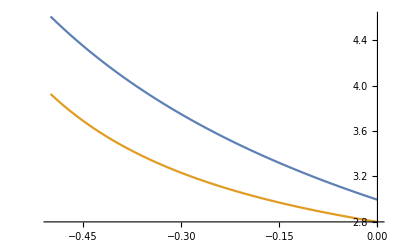

```mathematica
u=ArcCos[t2]/(2Pi);
Plot[{12u(1-e)/((1+e)Sin[2Pi u])/.{e->1/1000},2+(1+6e)/(Exp[a/3](a10[-1]+t2 a02[1]))/.{a->9.6,e->1/1000,e2->1/100}},{t2,-1/2,0}]
```

### Positivity of L2

```mathematica
num[1]=Pi Sin[2Pi x];
denom[1]=a x;
num[2]=-t1;
denom[2]=1;
num[3]=-Exp[a/3](b00 +a01 t2+a02 t2^2);
denom[3]=Exp[a/3](a10+a02 t2);
```

```mathematica
num[1]denom[2]denom[3]/.{t1->0,t2-> -1/5,x->1/4}
num[2]denom[1]denom[3]/.{t1->0,t2-> -1/5,x->1/4}
num[3]denom[1]denom[2]/.{t1->0,t2-> -1/5,x->1/4}
num[1]denom[2]denom[3]+num[2]denom[1]denom[3]+num[3]denom[1]denom[2]/.{t1->0,x->1/4}
Clear[t2]
```

(-a02/5+a10) ⅇ^(a/3) π

0

-1/4 a (-a01/5+a02/25+b00) ⅇ^(a/3)

ⅇ^(a/3) π (a10+a02 t2)-1/4 a ⅇ^(a/3) (b00+a01 t2+a02 t2^2)

Now let' s check positivity of ⅇ^(a/3) π (a10+a02 t2)-1/4 a ⅇ^(a/3) (b00+a01 t2+a02 t2^2)when we set t2=-1/5 and replace the coefficients with their corresponding bounds (ending up with a quadratic expression in a) . Since it’s quadratic in a, we just check the coefficient, value and

```mathematica
Pi ⅇ^(a/3) (a10[-1]+a02[1] t2)-1/4 a ⅇ^(a/3) (b00[1]+a01[-1] t2+a02[1] t2^2)/.t2->-1/5//Simplify
```

-1/(3600 π)(4 √3 a^2 (-1+59 e)+a (1118-880 √3+2 (1909+760 √3) e+261 e2) π+40 (29+254 e+18 e2) π^2)

```mathematica
ⅇ^(a/3) π (a10[-1]+a02[1] t2)-1/4 a ⅇ^(a/3) (b00[1]+a01[-1] t2+a02[1] t2^2)/.{t2->-1/5,a->9.6,e->1/1000,e2->1/100}
D[ⅇ^(a/3) π (a10[-1]+a02[1] t2)-1/4 a ⅇ^(a/3) (b00[1]+a01[-1] t2+a02[1] t2^2),a]/.{t2->-1/5,a->9.6,e->1/1000,e2->1/100}
```

0.0847354

0.121386

That completes the proof that L2 >= at (0. - .2)

Now at (-Sqrt[2]/2, 0)

We have to show that 4Pi Sqrt[2]/a (1+Exp[-a/4])/(3-(5-e)Exp[-a/4])+Sqrt[2]/2-b00[1]/a10[-1]>=0

```mathematica
Clear[num2,denom2]
```

```mathematica
expterm[c_]=4Pi Sqrt[2] (1+Exp[-c/4])/(3-(5-e)Exp[-c/4]);
Sqrt[2]/2 a Exp[a/3] a10[-1]//Simplify;
-Exp[a/3]b00[1]//Simplify;
L3[c_]:=expterm[c]Exp[a/3] a10[-1]+Sqrt[2]/2 a Exp[a/3] a10[-1]-a Exp[a/3]b00[1];
```

As detailed in the appendix with, it suffices to show the that L3[a_i]>=0 for a>=a_{i-1}, i>0with the sequence a_0=9.6,9.8,10,10.2,11,12,infinity. These are easy checks since L3 is quadratic in a for fixed c.

```mathematica
c=9.8;
b=9.6;
L3[c]/.{e->1/1000,e2->1/100}//Simplify
L3[c]/.{e->1/1000,e2->1/100,a->b}
D[L3[c],a]/.{e->1/1000,e2->1/100,a->b}
Clear[b,c]
```

-3.78042-0.260394 a+0.0684995 a^2

0.0327049

1.0548

```mathematica
c=10.;
b=9.8;
L3[c]/.{e->1/1000,e2->1/100}//Simplify
L3[c]/.{e->1/1000,e2->1/100,a->b}
D[L3[c],a]/.{e->1/1000,e2->1/100,a->b}
Clear[b,c]
```

-3.73518-0.276907 a+0.0684995 a^2

0.129823

1.06568

```mathematica
c=10.2;
b=10.;
L3[c]/.{e->1/1000,e2->1/100}//Simplify
L3[c]/.{e->1/1000,e2->1/100,a->b}
D[L3[c],a]/.{e->1/1000,e2->1/100,a->b}
Clear[b,c]
```

-3.69283-0.292367 a+0.0684995 a^2

0.233456

1.07762

```mathematica
c=11.;
b=10.2;
L3[c]/.{e->1/1000,e2->1/100}//Simplify
L3[c]/.{e->1/1000,e2->1/100,a->b}
D[L3[c],a]/.{e->1/1000,e2->1/100,a->b}
Clear[b,c]
```

-3.54815-0.345175 a+0.0684995 a^2

0.0577606

1.05222

```mathematica
c=12.;
b=11.;
L3[c]/.{e->1/1000,e2->1/100}//Simplify
L3[c]/.{e->1/1000,e2->1/100,a->b}
D[L3[c],a]/.{e->1/1000,e2->1/100,a->b}
Clear[b,c]
```

-3.41103-0.395221 a+0.0684995 a^2

0.529973

1.11177

```mathematica
c=Infinity;
b=12.;
L3[c]/.{e->1/1000,e2->1/100}//Simplify
L3[c]/.{e->1/1000,e2->1/100,a->b}
D[L3[c],a]/.{e->1/1000,e2->1/100,a->b}
Clear[b,c]
```

(√3 (-2002+2997 √2) a^2+(-23122-4527 √2+7992 √6) a π-12072 √2 π^2)/(18000 π)

0.252352

1.09133

### Negativity of N

As referenced in the appendix, it remains to show the following quantity is negative for a >= 9.6, and it' s quadratic in a, so we make the usual checks at a=9.6 to ensure this holds.

```mathematica
Exp[2a/3](a02[1](a00[1]+a10[1])-a01[-1]a10[-1])//Simplify
Exp[2a/3](a02[1](a00[1]+a10[1])-a01[-1]a10[-1])/.{a->9.6,e->1/1000,e2->1/100}
D[Exp[2a/3](a02[1](a00[1]+a10[1])-a01[-1]a10[-1]),a]/.{a->9.6,e->1/1000,e2->1/100}
```

1/(27 π^2)(-6 a^2 (1-10 e+e^2)+√3 a (13+10 e^2+9 e2+e (113+9 e2)) π-3 (1+6 e) (8+8 e-9 e2) π^2)

-0.351188

-0.158379